```mathematica
k:=5
rule=DSolve[{u''[x]-k*u[x]==2 - k*(x^2 - 1) - Cos[x] * (k + 1),u[0]==0,u[1]==Cos[1]},u,x]
f=First[u/.rule]
f[0.3]
Plot[u[x]/.rule,{x,-1,1}]
```

{{u→Function[{x},-1+x^2+Cos[x]]}}

Function[{x},-1+x^2+Cos[x]]

0.00500417

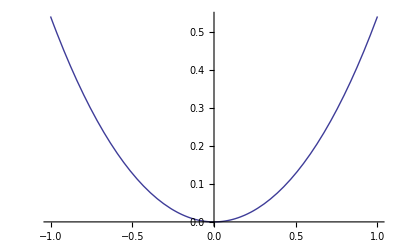
```mathematica
z-Graphics-
```

ReplaceAll::reps: {rule} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: "reps" will be suppressed during this calculation.

-Graphics-